NOTE: 
1. Load and run the file that creates the discontinued heat map. 
2. The eigenvalues below (L1-L4) are already evaluated with f = 1. 
3. You can control the fraction d/f with just d values. 
4. You will need to clear L1-L4 and reload the definitions between each run. 
5. Steps as follows: 
	(a)  Clear global env to make sure you are starting with a clean environment. Use command  ClearAll[“Global`*”]
	(b) Run the mathematica file with the redefined color function - this should load it in the global env. 
	(c) Load L1-L4 definitions
	(d) Evaluate at given d and z values
	(e) Update criteria for the region plot RegionPlot[{sp(1+c) > 2*0.1^(1/(1+(-0.5)))} : magenta is d, blue is z
	(f) Right click and select ‘save graphic as’ - PDF is default. 
	(g) Clear L1-L4
	(h) Repeat steps (c)-(g)

```mathematica
Clear[L1, L2, L3,L4]
```

```mathematica
L1 = 1/2 Re[-d+(d^(1/(1+z)))^(1+z) -((sp(1-c))^2 (-2 d^(1/(1+z))+sp(1+c)) z)/(sp(1+c))^3-1/(sp(1+c))^3(d^(1/(1+z)))^-z √(((d^(1/(1+z)))^(2 z) (4 (2 d^(1/(1+z))-(sp(1+c))) (sp(1-c))^2 (sp(1+c))^3 ((d^(1/(1+z)))^(1+z)+d z)+(-d (sp(1+c))^3+(d^(1/(1+z)))^(1+z) (sp(1+c))^3+(2 d^(1/(1+z))-sp(1+c)) (sp(1-c))^2 z)^2)))];
L2 = 1/2 Re[-d+(d^(1/(1+z)))^(1+z)-((sp(1-c))^2 (-2 d^(1/(1+z))+sp(1+c)) z)/(sp(1+c))^3+1/(sp(1+c))^3(d^(1/(1+z)))^-z √((d^(1/(1+z)))^(2 z) (4 (2 d^(1/(1+z))-sp(1+c)) (sp(1-c))^2 (sp(1+c))^3 ((d^(1/(1+z)))^(1+z)+d z)+(-d (sp(1+c))^3+(d^(1/(1+z)))^(1+z) (sp(1+c))^3+(2 d^(1/(1+z))-sp(1+c)) (sp(1-c))^2 z)^2))];

L3 = 1/2 Re[-d+(d^(1/(1+z)))^(1+z)-1/(sp(1+c))(-2 d^(1/(1+z)) (-1+z)+(sp(1+c)) z+(d^(1/(1+z)))^-z √((d^(1/(1+z)))^(2 z) ((sp(1+c))^2 (d-z)^2+d^(2/(1+z)) ((d^(1/(1+z)))^(2 z) (sp(1+c))^2+4 (-1+z)^2+4 (d^(1/(1+z)))^z (sp(1+c)) (3+z))-2 d^(1/(1+z)) (sp(1+c)) (-2 (d-z) (-1+z)+(d^(1/(1+z)))^z (sp(1+c)) (2+d+z)))))];
L4= 1/2 Re[-d+(d^(1/(1+z)))^(1+z)+1/(sp(1+c))(2 d^(1/(1+z)) (-1+z)-(sp(1+c)) z+(d^(1/(1+z)))^-z √((d^(1/(1+z)))^(2 z) ((sp(1+c))^2 (d-z)^2+d^(2/(1+z)) ((d^(1/(1+z)))^(2 z) (sp(1+c))^2+4 (-1+z)^2+4 (d^(1/(1+z)))^z (sp(1+c)) (3+z))-2 d^(1/(1+z)) (sp(1+c)) (-2 (d-z) (-1+z)+(d^(1/(1+z)))^z (sp(1+c)) (2+d+z)))))];
```

```mathematica
L1 = With[{d=0.1},{z=-0.15},Evaluate[L1]];
```

```mathematica
L2 = With[{d=0.1},{z=-0.15},Evaluate[L2]];
```

```mathematica
L3 = With[{d=0.1},{z=-0.15},Evaluate[L3]];
```

```mathematica
L4 = With[{d=0.1},{z=-0.15},Evaluate[L4]];
```

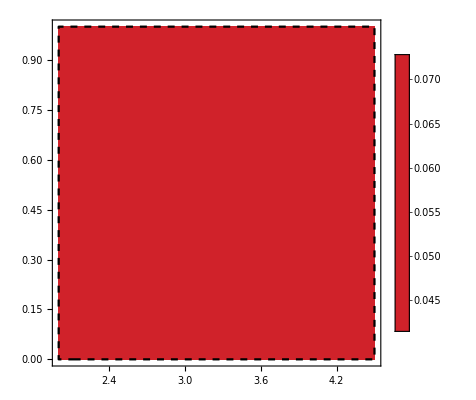

```mathematica
plot =Show[DensityPlot[Max[L1,L2,L3,L4], {sp, 2, 4.5}, {c, 0.0, 1},ColorFunction->(ColorData["TempMapDisconnectedGrey"][Piecewise[{{Rescale[#,{-0.02,-10^(-16)},{0,0.4166}],#<-10^(-16)},{Rescale[#,{-10^(-16),10^(-16)},{0.4166,0.5833}],-10^(-16)<#<10^(-16)},{Rescale[#,{10^(-16),0.03},{0.5833,1}],#>10^(-16)}}]] &), ColorFunctionScaling->False,PlotLegends->Automatic,Exclusions->None
], RegionPlot[{sp(1+c) > 2*0.1^(1/(1+(-0.5)))},{sp, 2, 4.5}, {c, 0.000, 1},PlotStyle->Opacity[0], BoundaryStyle->Directive[Black,Thick, Dashed]]]
```

```mathematica
Clear[L1, L2, L3,L4]
```